```mathematica
sparseError3D[f_,n_,stepsize_]:=Module[{values,ans,i,j,k,coeffs},
coeffs=sparseCoefficients[f,n,3];

If[stepsize≤ 2^-n,
For[i=0,i≤1,i+=2^-n,
For[j=0,j≤1,j+=2^-n,
For[k=0,k≤1,k+=2^-n,
values[{i,j,k}]=sparseReconstruct[coeffs,{i,j,k},n];
]]];
ans=Sqrt[stepsize^2 Sum[(f[{i,j,k}]-neighborAverage[values,{i,j,k},n])^2,{i,0,1,stepsize},{j,0,1,stepsize},{k,0,1,stepsize}]];
Return[ans]
,ans=Sqrt[stepsize^2 Sum[(f[{i,j,k}]-sparseReconstruct[coeffs,{i,j,k},n])^2,{i,0,1,stepsize},{j,0,1,stepsize},{k,0,1,stepsize}]];
Return[ans]]
]
```

```mathematica
sparseLengths3D=Table[Length[sparseIterate[n,3]],{n,1,12}];
hierLengths3D=Table[2^n+1,{n,1,10}]^3;
```

```mathematica
full3DError=Table[Timing[neighborError3D[Sin[Pi #[[1]]+#[[2]]+#[[3]]]&,n,.03]],{n,1,3}]
```

{{12.7761,1.00544},{13.0909,0.268294},{13.8125,0.068175}}

```mathematica
full3DError=Table[Timing[neighborError3D[Sin[Pi #[[1]]+#[[2]]+#[[3]]]&,n,.05]],{n,1,9}]
```

{{2.64123,0.797945},{2.50681,0.211164},{2.66204,0.0536385},{2.62425,0.0134631},{2.58405,0.00336914},{2.55858,0.000842495},{2.58237,0.000210637},{2.60771,0.00005266},{2.72298,0.000013165}}

```mathematica
sparse3DError=Table[sparseError3D[Sin[Pi #[[1]]+#[[2]]+#[[3]]]&,n,.1],{n,1,4}]
```

```mathematica
sparse3DError={0.9091405146221035,0.8333201879512053,0.26202690053231015,0.09300945147017446,0.03154424844272663,0.010529661362423235,0.0033890821898788503,0.0010720977352507261,0.00033123441192413035,0.00010084145624451475,0.000030196189799424187,8.934917544610521*^-6}
```

{0.909141,0.83332,0.262027,0.0930095,0.0315442,0.0105297,0.00338908,0.0010721,0.000331234,0.000100841,0.0000301962,8.93492×10^-6}

```mathematica
Timing[sparseError3D[Sin[Pi #[[1]]+#[[2]]+#[[3]]]&,12,.1]]
```

{271.987,8.93492×10^-6}

```mathematica
{0.326895,0.569186,2.729798,5.04923,9.803271,12.352008,17.956495,27.772584,43.526276,78.966349}
```

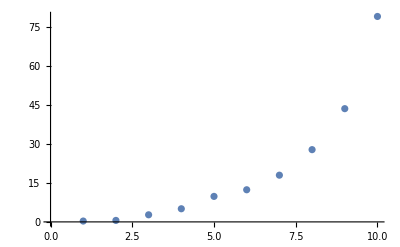

```mathematica
ListPlot[{0.326895,0.569186,2.729798,5.04923,9.803271,12.352008,17.956495,27.772584,43.526276,78.966349}]
```

```mathematica
sparse3DError2={1.128355851227411,1.1266221908945033,0.35651710696329286,0.12567322934684402,0.0432140728187158,0.01424855010071794,0.004618081552104229}
```

{1.12836,1.12662,0.356517,0.125673,0.0432141,0.0142486,0.00461808}

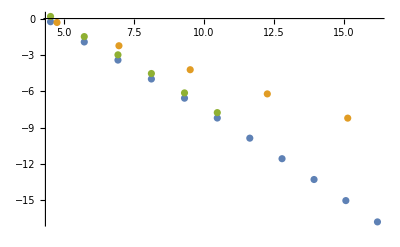

```mathematica
Show[ListPlot[{Table[{sparseLengths3D[[n]],sparse3DError[[n]]}//Log2,{n,2,12}],Table[{hierLengths3D[[n]],full3DError[[n,2]]}//Log2,{n,1,5}],Table[{sparseLengths3D[[n]],sparse3DError2[[n]]}//Log2,{n,2,7}]}]]
```

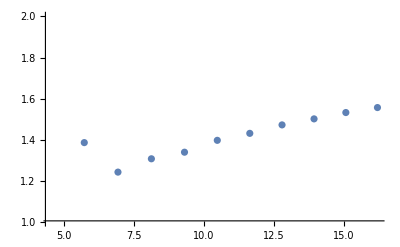

```mathematica
ListPlot[Table[{Log2[sparseLengths3D[[n]]],-(Log2[sparse3DError⟦n⟧]-Log2[sparse3DError⟦n-1⟧])/(Log2[sparseLengths3D[[n]]]-Log2[sparseLengths3D[[n-1]]])},{n,2,12}],PlotRange->{1,2}]
```

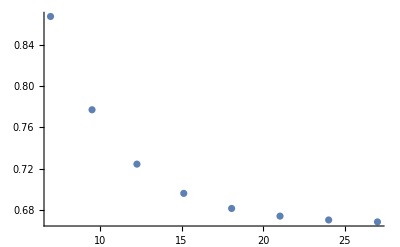

```mathematica
ListPlot[Table[{Log2[hierLengths3D[[n]]],-(Log2[full3DError⟦n,2⟧]-Log2[full3DError⟦n-1,2⟧])/(Log2[hierLengths3D⟦n⟧]-Log2[hierLengths3D⟦n-1⟧])},{n,2,9}]]
```

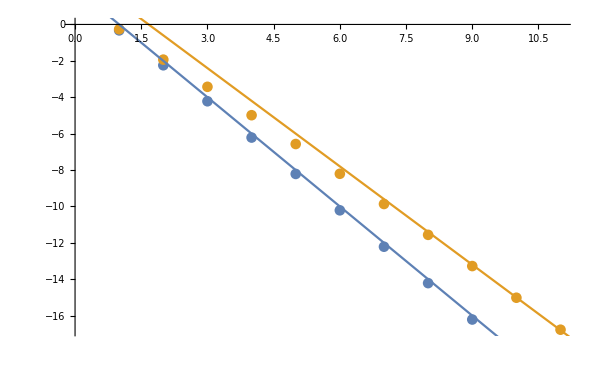

```mathematica
Show[ListPlot[{Table[full3DError[[n,2]]//Log2,{n,1,9}],Table[sparse3DError[[n]]//Log2,{n,2,12}]}],Plot[{-2x+2,-1.8x+3},{x,0,12}]]
```

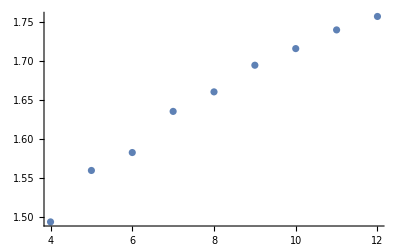

```mathematica
ListPlot[Table[{n,-(Log2[sparse3DError⟦n⟧]-Log2[sparse3DError⟦n-1⟧])/1},{n,4,12}]]
```

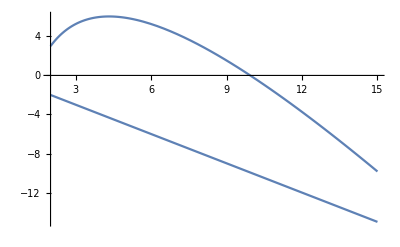

```mathematica
Plot[{(x^3/2^x)^3,1/2^(x)}//Log2,{x,2,15}]
```

```mathematica
Limit[D[Log2[(x^3/2^x)^2],x],x->Infinity]
Limit[D[Log2[(x^3/2^x)^3],x],x->Infinity]
```

-2

-3